```mathematica
(* L1-norm calculation for MEMS-state under correlated ADC with memory: *)
(* Defining uncorrelated-ADC Kraus Operators for single qubit: *)
SetDirectory[NotebookDirectory[]];
ClearAll[g,γ, μ,  p];
A0={{1, 0},{0,√(1-p)}};
A1={{0,√p}, {0, 0}};
A0//MatrixForm;
A1//MatrixForm;

(* Uncorrelated-ADC Kraus operators for two-qubits: *)
A00=KroneckerProduct[A0,A0];
A01=KroneckerProduct[A0,A1];
A10=KroneckerProduct[A1,A0];
A11=KroneckerProduct[A1,A1];

(* Correlated-ADC Kraus operators for two qubits: *)
B00 = {{√(1-p), 0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
B11= {{0,0,0,0},{0,0,0,0},{0,0,0,0},{√p,0,0,0}};
B00//MatrixForm;
B11//MatrixForm;

(* Checking the completeness of the Kraus operators: *)
A={A00,A01,A10,A11};
B={B00,B11};
FullSimplify[Sum[Transpose[A[[i]]].A[[i]],{i,1,4}]]//MatrixForm;
FullSimplify[Sum[Transpose[B[[i]]].B[[i]],{i,1,2}]]//MatrixForm;
```

```mathematica
(* MEMS-state density Matrix *)
ClearAll[g,γ,p,μ];
 ρ={{g,0,0,γ/2},{0,1-2g,0,0},{0,0,0,0},{γ/2,0,0,g}};
ρ//MatrixForm;
Tr[ρ];

(* Density Matrix after evolution in correlated-ADC: *)
ρ1=(1-μ)*Sum[A[[i]].ρ.Transpose[A[[i]]],{i,1,4}]+μ*Sum[B[[i]].ρ.Transpose[B[[i]]],{i,1,2}]; 
Simplify[Tr[ρ1]];
ρ1//MatrixForm;
```

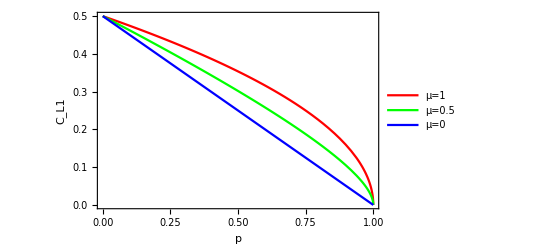

```mathematica
(*L1 norm of coherence: *)
ClearAll[g,γ, μ,  p];
γ=0.5;
g=1/3;
L1=Sum[If[i!=j,Abs[ρ1[[i,j]]],0],{i,1,4},{j,1,4}];
L1fig1=Plot[Evaluate@Table[L1,{μ,{1,0.5,0}}],{p,0,1},FrameLabel->{"p","C_L1"},PlotLegends->Placed[{"μ=1", "μ=0.5","μ=0"},{0.9,0.8}],PlotStyle->{Red, Green, Blue},Frame-> True, FrameStyle->Directive[Black,12]]
Export["L1fig1_ADC.pdf",L1fig1];
```

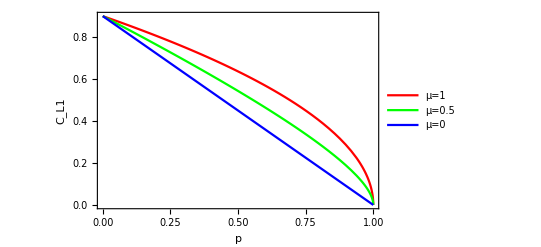

```mathematica
(* L1 norm of coherence: *)
ClearAll[g,γ, μ,  p];
γ=0.9;
g=γ/2;
L1=Sum[If[i!=j,Abs[ρ1[[i,j]]],0],{i,1,4},{j,1,4}];
L1fig2=Plot[Evaluate@Table[L1,{μ,{1,0.5,0}}],{p,0,1},FrameLabel->{"p","C_L1"},PlotLegends->Placed[{"μ=1", "μ=0.5","μ=0"},{0.9,0.8}],PlotStyle->{Red, Green, Blue},Frame-> True, FrameStyle->Directive[Black,12]]
Export["L1fig2_ADC.pdf",L1fig2];
```

```mathematica
(* L1-norm in 3D plot*)
ClearAll[g,γ, μ,  p];
γ=0.5;
g=1/3;
L1=Sum[If[i!=j,Abs[ρ1[[i,j]]],0],{i,1,4},{j,1,4}];
L1norm3D=Plot3D[L1,{p,0,1},{μ,0,1},AxesLabel->{"p","μ","C_L1 "},AxesStyle->Directive[Bold,Black, 12],ColorFunction->Function[{x,y,z},Hue[Mod[z,1]]],ColorFunctionScaling->False]
Export["L1norm3D_ADC.pdf",L1norm3D];
```

-Graphics3D-

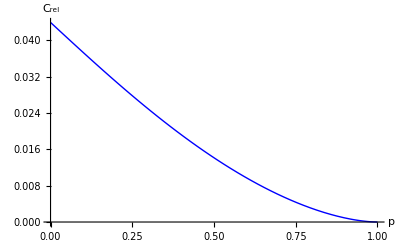

```mathematica
(* Relative Entropy of Coherence for a two-qubit density Matrix *)
CR[ρ_]:=Module[{dg,eg,VNdg,VNeg,Cr},
dg=Diagonal[ρ];
VNdg=Sum[If[dg[[i]]≠0,-dg[[i]]*Log[2,dg[[i]]],0],{i,1,Length[dg]}];
eg=Eigenvalues[ρ];
 VNeg=Sum[If[eg[[i]]≠0,-eg[[i]]*Log[2,eg[[i]]],0],{i,1,Length[eg]}];
Cr=N[VNdg-VNeg]; 
Cr];

ClearAll[g,γ, μ,  p];
γ=1/5;
g=1/3;
μ=0;
Plot[CR[ρ1],{p,0,1},PlotStyle->Directive[12,Thick,Blue],AxesLabel->{"p","C_rel"}]
```

```mathematica
(*  Concurrence Module *)
rhotilde[state_]:=(KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]).(Conjugate[state].(KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]));
  rhocon[state_]:=state.rhotilde[state];
eigensqrt[state_]:=Re[Sqrt[Eigenvalues[rhocon[state]]]];
order[state_]:=Sort[eigensqrt[state],Greater];
concurr[state_]:=Max[0,order[state][[1]]-order[state][[2]]-order[state][[3]]-order[state][[4]]];
```

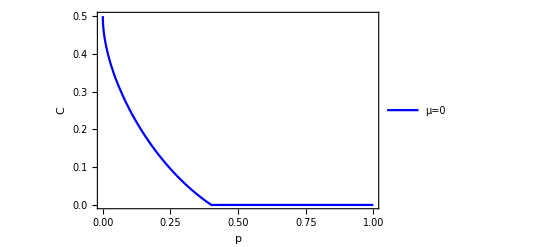

```mathematica
ClearAll[g,γ, μ,  p]; 
(* γ=0.9; g=γ/2; *)
γ=0.5;
g=1/3; 
μ=0;
p1=Plot[N[concurr[ρ1]],{p,0,1},FrameLabel->{"p","C"},PlotRange->All,LabelStyle->{FontSize->10, Black,Bold},PlotLegends->Placed[{"μ=0"},{0.9,0.6}],PlotRange->{0,0.8},PlotStyle->Blue,Frame->True]
```

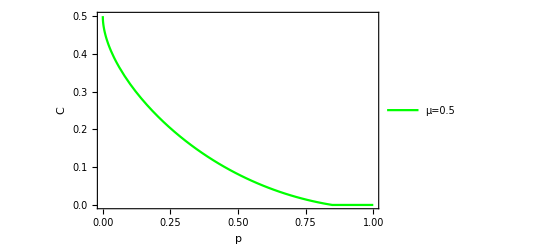

```mathematica
ClearAll[g,γ, μ,  p];
γ=0.5;
g=1/3;
μ=0.5;
p2=Plot[N[concurr[ρ1]],{p,0,1},FrameLabel->{"p","C"},PlotRange->All,LabelStyle->{FontSize->10, Black,Bold},PlotLegends->Placed[{"μ=0.5"},{0.9,0.7}],PlotRange->{0,0.8},PlotStyle->Green,Frame->True]
```

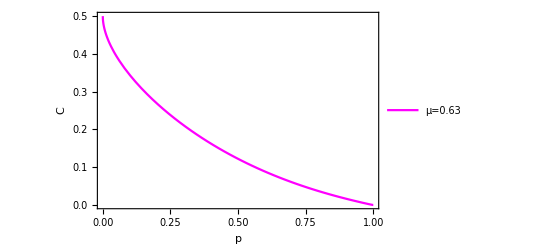

```mathematica
ClearAll[g,γ, μ,  p]; 
γ=0.5;
g=1/3;
μ=0.63;
p3=Plot[N[concurr[ρ1]],{p,0,1},FrameLabel->{"p","C"},PlotRange->All,LabelStyle->{FontSize->10, Black,Bold},PlotLegends->Placed[{"μ=0.63"},{0.9,0.8}],PlotRange->{0,0.8}, PlotStyle->Magenta,Frame->True]
```

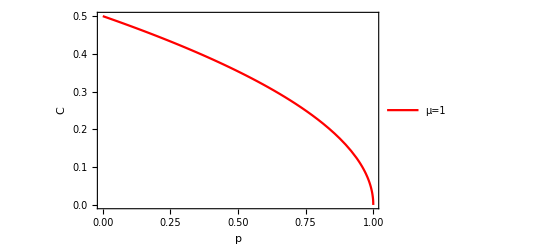

```mathematica
ClearAll[g,γ, μ,  p]; 
γ=0.5;
g=1/3;
μ=1;
p4=Plot[N[concurr[ρ1]],{p,0,1},FrameLabel->{"p","C"},PlotRange->All,LabelStyle->{FontSize->10, Black,Bold},PlotLegends->Placed[{"μ=1"},{0.9,0.9}],PlotRange->{0,0.8}, PlotStyle->Red,Frame->True]
```

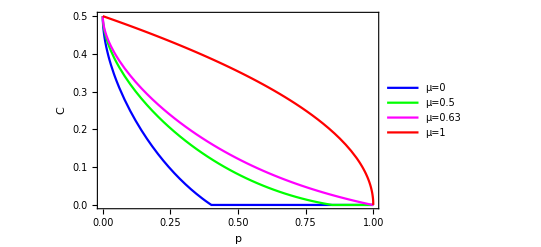

```mathematica
p5=Show[p1,p2,p3,p4, PlotRange->All,FrameLabel->{"p","C"}, FrameStyle->Directive[Black,12],Frame-> True]
Export["Conc_ADC.pdf",p5];
```

```mathematica
(* Concurrence in 3D plot *)
ClearAll[g,γ, μ,  p];
γ=0.5;
g=1/3;
Conc3D=Plot3D[concurr[ρ1],{p,0,1},{μ,0,1},AxesLabel->{"p","μ","C "},AxesStyle->Directive[Bold,Black, 12],ColorFunction->Function[{x,y,z},Hue[Mod[z,1]]],ColorFunctionScaling->False]
(* ColorFunction->Function[{x,y,z},Hue[z]] *)
Export["Conc3D_ADC.pdf",Conc3D];
```

-Graphics3D-

```mathematica
(* Purity plot in 3D: *)
ClearAll[g,γ, μ,  p]; 
γ=0.5;
g=1/3;
Purity3D=Plot3D[Tr[ρ1.ρ1],{p,0,1},{μ,0,1},AxesLabel->{"p","μ","Purity "},AxesStyle->Directive[Bold,Black, 12],ColorFunction->Function[{x,y,z},Hue[Mod[z,1]]],ColorFunctionScaling->False,PlotRange->All]
(* ColorFunction->Function[{x,y,z},Hue[z]] *)
Export["Purity3D_ADC.pdf",Purity3D];
```

-Graphics3D-